# Energetski kazalniki, Slovenija, letno

Pridobivanje podatkov

```mathematica
(*pridobil podatke, dodal stolpec z "vrsto" in pa vsemi letnicami ter zamnejal "..." z 0, kjer je bilo to potrebno*)
```

```mathematica
podatki =Import["C:\\Users\\matij\\ROM-projektna-naloga\\tabela.csv","Table","FieldSeparators"->";",CharacterEncoding->"WindowsEastEurope",HeaderLines->1]//Prepend[#,{"Vrsta",2000,2001,2002,2003,2004,2005,2006,2007, 2008, 2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021}]&//Map[If[#=="...",0,#]&,#,{2}]&//Transpose;
```

```mathematica
tabelaPodatkov=ResourceFunction["DatasetWithHeaders"][podatki]
```

```mathematica
Skupni delež OVE
```

```mathematica
delezi=tabelaPodatkov//Query[All,{1,16}]//Map[If[#=="-",0,#]&,#,{2}]&
```

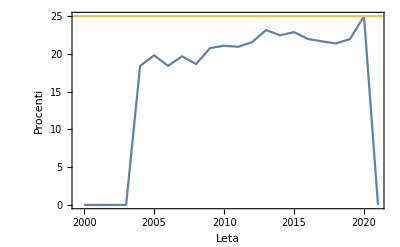

```mathematica
ListLinePlot[delezi, GridLines->{None,{25}},
GridLinesStyle->Directive[AbsoluteThickness[3/2],ColorData[88,8]],Frame->True,FrameLabel->{{"Procenti",""},{"Leta","Skupni delež OVE [%]"}},BaseStyle->{FontSize->15}]
```

```mathematica
OVE Transport
```

```mathematica
leta={2000,2001,2002,2003,2004,2005,2006,2007, 2008, 2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021}
```

{2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021}

```mathematica
deleziTransporta=tabelaPodatkov//Query[All,{1,15}]//Map[If[#=="-",0,#]&,#,{2}]&
```

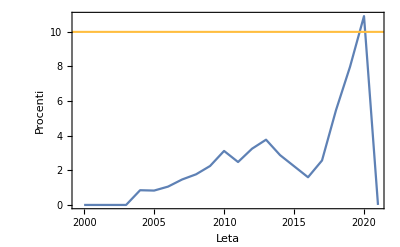

```mathematica
ListLinePlot[deleziTransporta, GridLines->{None,{10}},
GridLinesStyle->Directive[AbsoluteThickness[3/2],ColorData[88,8]],Frame->True,FrameLabel->{{"Procenti",""},{"Leta","OVE Transport [%]"}},BaseStyle->{FontSize->15}]
```

```mathematica
Energetska odvisnost
```

```mathematica
odvisnost=tabelaPodatkov//Query[All,{1,5}]//Map[If[#=="-",0,#]&,#,{2}]&
```

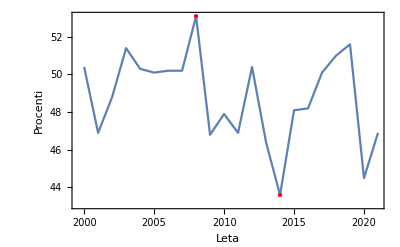

```mathematica
ListLinePlot[odvisnost,Epilog->{Red,PointSize@Large,Point[{{2014,43.6},{2008,53.1}}]},Frame->True,FrameLabel->{{"Procenti",""},{"Leta","Energetska odvisnost [%]"}},BaseStyle->{FontSize->15},BaseStyle->{FontSize->15}]
```

```mathematica
samoVrednosti=tabelaPodatkov//Query[All,{5}]//Map[If[#=="-",0,#]&,#,{2}]&;
```

```mathematica
leta={2000,2001,2002,2003,2004,2005,2006,2007, 2008, 2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021};
```

```mathematica
BarChart[samoVrednosti,ChartLabels->{leta},ChartStyle->40,Frame->True,FrameLabel->{{"Procenti",""},{"Leta","Energetska odvisnost [%]"}},BaseStyle->{FontSize->14},ImageSize->900]
```